```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];

data=Import["S1.csv"];
```

```mathematica
data[[;;59]]//TableForm
data0=data[[60;;,{1,2}]];
```

Machine Module | N9343C | CN06050179 |  | 
MCU Version | A.06.27 |  |  | 
DSP Version | A.04.00.11 SA |  |  | 
FPGA Version | A.02.80 |  |  | 
16:04:54 02.20.2018 |  |  |  | 
Y Axis Scale | LOG |  |  | 
Y Axis Unit | dBm |  |  | 
Impedance | 50 |  |  | 
Number of Points | 461 |  |  | 
Sweep Time(s) | 6.57041 | AUTO |  | 
Start Frequency | 2.99999×10^7 |  |  | 
Stop Frequency | 3.15×10^7 |  |  | 
Frequency Offset | 0. |  |  | 
Average Type | Power |  |  | 
RBW | 100. | MAN |  | 
VBW | 100. | AUTO |  | 
Sweep Type | Continuous |  |  | 
Sweep Mode | Sweep |  |  | 
Speed | Normal |  |  | 
PreAmp State | OFF |  |  | 
Ref Level | -27. |  |  | 
Attenuation | 10 | AUTO |  | 
Ref Level Offset | 0. |  |  | 
X Axis Units | Hz |  |  | 
HiSensitive | OFF |  |  | 
Trigger Source | FreeRun |  |  | 
Trigger Level | 0. |  |  | 
Trigger Slope | RISE |  |  | 
Trigger Delay | 0. | OFF |  | 
Gate Sweep | OFF |  |  | 
Gate View | OFF |  |  | 
Gate Delay | 0.00228 |  |  | 
Gate Length | 0.00084 |  |  | 
Gate Source | External |  |  | 
Burst Level | -20. |  |  | 
Burst Trigger Slope | Rise |  |  | 
Timer Period | 0.00312 |  |  | 
Timer Offset | 0. |  |  | 
Sync Source | Off |  |  | 
Apply Corrections | OFF |  |  | 
Antenna Unit | OFF |  |  | 
Correction1 | Off |  |  | 
Correction2 | Off |  |  | 
Correction3 | Off |  |  | 
Correction4 | Off |  |  | 
Marker Information |  |  |  | 
Marker | Trace | Type | X Axis | Amplitude
M1 | 1 | Frequency | 29.999 MHz | -25.88 dBm
CISPR Filter | Normal RBW | Dwell Time(s) | 0.5 | AUTO
Trace Math | Off |  |  | 
Trace Math By | Log Power |  |  | 
Trace Variable A | Trace1 |  |  | 
Trace Variable B | Trace2 |  |  | 
Trace Variable C | Trace3 |  |  | 
Trace Name | Trace1 |  |  | 
Trace Count | 1 |  |  | 
Trace Type | Clear Write |  |  | 
Trace Detector | Average |  |  | 
Trace Data |  |  |  |

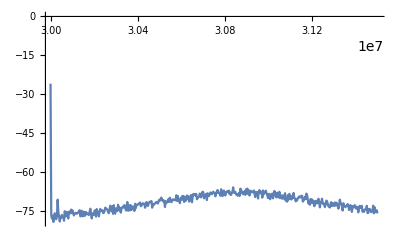

```mathematica
ListPlot[data0,Joined->True,PlotRange->All]
cutoff=-60;
posDC=Flatten[Position[Boole[Positive[data0[[;;,2]]-cutoff]],1]][[1]];
```

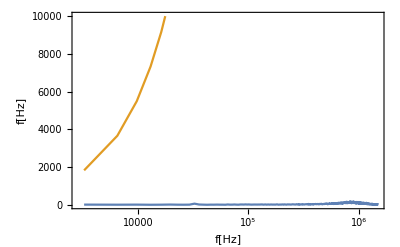

```mathematica
Clear[att];
att=10;(*attenutation in dB *)
W[x_]:=10^((x+att-30)/10); (*power in W given in dBm/Hz*)
Vsq[x_]:=W[x] 50 ;(*voltage^2 in V^2 given in V^2/Hz*)
us=10^-6;
τ=3.7555us;
FWHM=1/(π τ);
fpkpk=FWHM/√3;
Vpkpk=1.25;
Hzsq[x_]:=(fpkpk/Vpkpk)^2 Vsq[x];(*freq^2 in Hz^2 given in Hz^2/Hz*)

f=data0[[;;,1]];
f=f-f[[posDC]]; (*move carrier to DC*)
h0=Hzsq[data0[[;;,2]]]; (*frequency noise amplitude*)

rbw=f[[2]]-f[[1]];

β[f_]:=8Log[2]f/π^2;
βlist=Table[{ff,β[ff]},{ff,f}];
data1=Thread[{f,h0}];

dataDiff=Thread[{f,h0-βlist[[;;,2]]}];

Show[{
ListLogLinearPlot[{data1,βlist},Joined->True,Axes->False,Frame->True,FrameLabel->{"f[Hz]","f[Hz]"},PlotRange->{All,{0,10000}}]
}]
```

```mathematica
linewidth=Total[Boole[Positive[dataDiff[[posDC+1;;,2]]]]data1[[posDC+1;;,2]]rbw]

(*eq 10 from paper,ignoring 0 frequency bin*)
```

0.